```mathematica
(*Legendre associated polynomial function*)LGP[j_,m_,θ_]:=N[Sqrt[(2 j+1)/(4 π) (j-m)!/(j+m)!] LegendreP[j,m,Cos[θ]]]

(*Clebsh-Gordan function*)
CG[j_,m_,J_,M_]:=If[Abs[M-m]<=j&&Abs[M]<=J,N[ClebschGordan[{j,m},{j,M-m},{J,M}]],0]

(*Ladder operators*)
Cplus[j_,m_]:=N[Sqrt[j (j+1)-m (m+1)]]
Cminus[j_,m_]:=N[Sqrt[j (j+1)-m (m-1)]]
```

```mathematica
(*φ integral when O=Subscript[Z,1]Subscript[Z,2]*)
IntZZ[m_,n_]:=Module[{numerator,denominator,result},If[m==n,result=0,(*otherwise,if m≠n*)numerator=I (-1+E^(I (-m+n) π/2))^3 (1+E^(I (-m+n) π/2));
denominator=m-n;
result=numerator/denominator];
N[result]]

(*φ integral when O=Subscript[X,1]Subscript[X,2]*)
IntXX[m_,n_]:=Module[{numerator,denominator,result},If[m==n,result=1/2 E^(-(3/2) I m π) (1+E^(I m π)+E^(2 I m π)+E^(3 I m π)) π,(*otherwise,if m≠n*)result=-(1/(m-n)) I E^(-2 I m π) (E^((I m π)/2)-E^((I n π)/2)+E^(1/2 I (2 m+n) π)-E^(1/2 I (m+2 n) π)+E^(1/2 I (3 m+2 n) π)-E^(1/2 I (2 m+3 n) π)+E^(1/2 I (4 m+3 n) π)-E^(1/2 I (3 m+4 n) π));];
N[result]]

Integral[j_,m_,n_]:=Module[{integralPhi,integralTheta,result},(*Check initial conditions:if|m|>j or|n|>j,return 0*)If[Abs[m]>j||Abs[n]>j,Return[0]];
integralPhi=IntXX[m,n];
If[integralPhi==0,result=0,integralTheta=NIntegrate[LGP[j,m,θ]*LGP[j,n,θ]*Sin[θ],{θ,0,π}];
result=N[Chop[integralPhi*integralTheta]]];
Return[result]]
```

```mathematica
(*TrAxComplete function*)
TrAxComplete[j_,J_]:=Module[{sumM,result,cgm1,cgm2,term},If[J>2*j,Return[0]];
(*Assicurati che tutti i termini siano numerici*)sumM=Table[cgm1=N[CG[j,m,J,M-m]];(*Forza la valutazione numerica*)cgm2=N[CG[j,n,J,M-n]];(*Forza la valutazione numerica*)If[cgm1!=0&&cgm2!=0,term=N[Cplus[j,m]*Integral[j,m+1,n]+Cminus[j,m]*Integral[j,m-1,n]-Cplus[j,n]*Integral[j,m,n+1]-Cminus[j,n]*Integral[j,m,n-1]];(*Forza la valutazione numerica*)If[term!=0,resultTerm=N[cgm1*cgm2*term*(Cplus[j,M-m]*Integral[j,M-m+1,M-n]+Cminus[j,M-m]*Integral[j,M-m-1,M-n]-Cplus[j,M-n]*Integral[j,M-m,M-n+1]-Cminus[j,M-n]*Integral[j,M-m,M-n-1])];(*Forza la valutazione numerica*)resultTerm,0],0],{m,-j,j},{n,-j,j},{M,-J,J}];
result=(1/4)*Total[Total[Total[sumM]]];
Chop[N[result]] (*Forza la valutazione numerica finale*)]

TrComplete =TrAxComplete[2,4];

TrComplete
```

-5.815

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.8777}. NIntegrate obtained 6.28295×10^-17 and 3.44659×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.8777}. NIntegrate obtained -6.57569×10^-17 and 3.36527×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

j = 8, J = 0, TrComplete = 0.

j = 8, J = 1, TrComplete = 0.25 (0.+cgm1$172807 cgm2$172807 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$5979917+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$5979919-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$5979921-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$5979923) term$172807+cgm1$172807 cgm2$172807 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$5981383+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$5981385-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$5981387-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$5981389) term$172807+cgm1$172807 cgm2$172807 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$5982811+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$5982813-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$5982815-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$5982817) term$172807+cgm1$172807 cgm2$172807 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$5985027+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$5985029-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$5985031-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$5985033) term$172807+cgm1$172807 cgm2$172807 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$5986455+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$5986457-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$5986459-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$5986461) term$172807+cgm1$172807 cgm2$172807 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$5988671+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$5988673-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$5988675-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$5988677) term$172807+cgm1$172807 cgm2$172807 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$5990157+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$5990159-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$5990161-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$5990163) term$172807+cgm1$172807 cgm2$172807 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$5991623+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$5991625-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$5991627-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$5991629) term$172807)

j = 8, J = 2, TrComplete = 0.25 (0.+cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$5993557+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$5993559-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$5993561-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$5993563) term$173726+cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$5994981+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$5994983-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$5994985-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$5994987) term$173726+cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$5996247+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$5996249-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$5996251-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$5996253) term$173726+2. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$5997553+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$5997555-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$5997557-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$5997559) term$173726+2. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$5998899+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$5998901-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$5998903-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$5998905) term$173726+2. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6000953+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6000955-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6000957-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6000959) term$173726+3. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6002399+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6002401-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6002403-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6002405) term$173726+2. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6003667+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6003669-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6003671-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6003673) term$173726+cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6005171+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6005173-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6005175-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6005177) term$173726+3. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6006597+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6006599-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6006601-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6006603) term$173726+4. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6008025+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6008027-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6008029-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6008031) term$173726+2. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6009313+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6009315-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6009317-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6009319) term$173726+2. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6011367+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6011369-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6011371-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6011373) term$173726+4. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6012775+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6012777-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6012779-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6012781) term$173726+4. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6014203+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6014205-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6014207-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6014209) term$173726+2. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6015589+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6015591-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6015593-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6015595) term$173726+2. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6017525+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6017527-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6017529-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6017531) term$173726+4. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6018953+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6018955-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6018957-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6018959) term$173726+3. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6020439+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6020441-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6020443-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6020445) term$173726+cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6021923+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6021925-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6021927-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6021929) term$173726+2. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6023171+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6023173-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6023175-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6023177) term$173726+3. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6024637+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6024639-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6024641-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6024643) term$173726+2. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6026023+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6026025-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6026027-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6026029) term$173726+2. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6028057+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6028059-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6028061-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6028063) term$173726+2. cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6029423+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6029425-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6029427-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6029429) term$173726+cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6030669+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6030671-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6030673-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6030675) term$173726+cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6032113+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6032115-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6032117-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6032119) term$173726+cgm1$173726 cgm2$173726 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6033359+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6033361-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6033363-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6033365) term$173726)

j = 8, J = 3, TrComplete = 0.25 (0.+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6034993+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6034995-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6034997-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6034999) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6036257+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6036259-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6036261-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6036263) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6037641+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6037643-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6037645-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6037647) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6038807+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6038809-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6038811-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6038813) term$237195+3. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6039973+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6039975-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6039977-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6039979) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6041397+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6041399-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6041401-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6041403) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6042643+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6042645-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6042647-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6042649) term$237195+3. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6044497+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6044499-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6044501-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6044503) term$237195+4. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6045803+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6045805-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6045807-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6045809) term$237195+3. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6047149+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6047151-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6047153-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6047155) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6048317+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6048319-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6048321-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6048323) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6049661+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6049663-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6049665-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6049667) term$237195+4. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6050967+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6050969-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6050971-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6050973) term$237195+4. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6052413+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6052415-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6052417-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6052419) term$237195+4. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6053681+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6053683-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6053685-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6053687) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6054869+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6054871-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6054873-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6054875) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6056961+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6056963-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6056965-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6056967) term$237195+4. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6058387+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6058389-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6058391-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6058393) term$237195+4. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6059815+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6059817-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6059819-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6059821) term$237195+4. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6061103+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6061105-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6061107-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6061109) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6062389+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6062391-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6062393-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6062395) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6063773+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6063775-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6063777-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6063779) term$237195+3. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6065079+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6065081-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6065083-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6065085) term$237195+4. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6066487+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6066489-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6066491-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6066493) term$237195+4. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6067915+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6067917-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6067919-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6067921) term$237195+3. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6069301+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6069303-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6069305-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6069307) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6070725+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6070727-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6070729-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6070731) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6071931+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6071933-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6071935-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6071937) term$237195+4. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6073159+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6073161-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6073163-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6073165) term$237195+4. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6074587+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6074589-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6074591-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6074593) term$237195+4. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6076073+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6076075-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6076077-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6076079) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6077557+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6077559-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6077561-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6077563) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6079333+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6079335-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6079337-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6079339) term$237195+4. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6080581+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6080583-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6080585-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6080587) term$237195+4. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6082047+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6082049-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6082051-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6082053) term$237195+4. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6083433+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6083435-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6083437-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6083439) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6084777+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6084779-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6084781-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6084783) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6085885+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6085887-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6085889-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6085891) term$237195+3. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6087231+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6087233-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6087235-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6087237) term$237195+4. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6088597+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6088599-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6088601-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6088603) term$237195+3. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6089843+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6089845-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6089847-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6089849) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6091677+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6091679-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6091681-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6091683) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6093121+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6093123-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6093125-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6093127) term$237195+3. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6094367+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6094369-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6094371-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6094373) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6095473+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6095475-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6095477-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6095479) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6096857+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6096859-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6096861-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6096863) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6098181+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6098183-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6098185-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6098187) term$237195+2. cgm1$237195 cgm2$237195 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6099287+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6099289-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6099291-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6099293) term$237195)

j = 8, J = 4, TrComplete = 0.25 (0.+cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6101331+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6101333-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6101335-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6101337) term$243962+cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6102577+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6102579-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6102581-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6102583) term$243962+2. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6104222+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6104224-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6104226-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6104228) term$243962+2. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6105486+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6105488-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6105490-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6105492) term$243962+2. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6106870+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6106872-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6106874-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6106876) term$243962+cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6108194+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6108196-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6108198-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6108200) term$243962+2. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6109211+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6109213-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6109215-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6109217) term$243962+5. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6110377+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6110379-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6110381-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6110383) term$243962+5. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6111801+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6111803-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6111805-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6111807) term$243962+4. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6113047+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6113049-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6113051-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6113053) term$243962+2. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6114293+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6114295-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6114297-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6114299) term$243962+cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6115468+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6115470-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6115472-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6115474) term$243962+5. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6116634+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6116636-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6116638-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6116640) term$243962+6. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6117940+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6117942-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6117944-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6117946) term$243962+6. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6119286+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6119288-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6119290-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6119292) term$243962+4. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6120454+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6120456-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6120458-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6120460) term$243962+2. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6121700+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6121702-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6121704-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6121706) term$243962+2. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6122955+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6122957-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6122959-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6122961) term$243962+6. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6124261+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6124263-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6124265-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6124267) term$243962+7. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6125707+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6125709-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6125711-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6125713) term$243962+6. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6126975+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6126977-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6126979-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6126981) term$243962+4. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6128163+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6128165-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6128167-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6128169) term$243962+cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6129507+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6129509-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6129511-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6129513) term$243962+cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6130154+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6130156-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6130158-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6130160) term$243962+5. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6131558+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6131560-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6131562-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6131564) term$243962+7. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6132984+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6132986-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6132988-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6132990) term$243962+8. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6134412+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6134414-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6134416-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6134418) term$243962+6. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6135700+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6135702-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6135704-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6135706) term$243962+4. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6136986+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6136988-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6136990-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6136992) term$243962+2. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6138989+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6138991-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6138993-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6138995) term$243962+6. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6140295+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6140297-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6140299-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6140301) term$243962+8. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6141703+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6141705-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6141707-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6141709) term$243962+8. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6143131+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6143133-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6143135-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6143137) term$243962+6. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6144517+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6144519-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6144521-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6144523) term$243962+2. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6145941+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6145943-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6145945-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6145947) term$243962+4. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6147766+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6147768-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6147770-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6147772) term$243962+6. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6148994+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6148996-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6148998-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6149000) term$243962+8. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6150422+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6150424-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6150426-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6150428) term$243962+7. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6151908+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6151910-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6151912-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6151914) term$243962+5. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6153392+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6153394-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6153396-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6153398) term$243962+cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6154707+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6154709-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6154711-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6154713) term$243962+cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6155363+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6155365-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6155367-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6155369) term$243962+4. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6156471+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6156473-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6156475-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6156477) term$243962+6. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6157719+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6157721-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6157723-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6157725) term$243962+7. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6159185+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6159187-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6159189-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6159191) term$243962+6. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6160571+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6160573-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6160575-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6160577) term$243962+2. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6161915+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6161917-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6161919-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6161921) term$243962+2. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6163072+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6163074-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6163076-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6163078) term$243962+4. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6164180+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6164182-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6164184-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6164186) term$243962+6. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6165526+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6165528-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6165530-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6165532) term$243962+6. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6166892+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6166894-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6166896-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6166898) term$243962+5. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6168138+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6168140-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6168142-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6168144) term$243962+cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6169313+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6169315-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6169317-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6169319) term$243962+2. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6170479+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6170481-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6170483-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6170485) term$243962+4. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6171705+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6171707-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6171709-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6171711) term$243962+5. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6173149+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6173151-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6173153-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6173155) term$243962+5. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6174395+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6174397-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6174399-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6174401) term$243962+2. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6175501+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6175503-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6175505-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6175507) term$243962+cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6176676+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6176678-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6176680-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6176682) term$243962+2. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6178060+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6178062-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6178064-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6178066) term$243962+2. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6179384+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6179386-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6179388-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6179390) term$243962+2. cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6180490+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6180492-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6180494-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6180496) term$243962+cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6182284+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6182286-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6182288-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6182290) term$243962+cgm1$243962 cgm2$243962 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6183450+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6183452-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6183454-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6183456) term$243962)

j = 8, J = 5, TrComplete = 0.25 (0.+2. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6185258+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6185260-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6185262-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6185264) term$299619+2. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6186344+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6186346-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6186348-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6186350) term$299619+2. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6187590+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6187592-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6187594-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6187596) term$299619+cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6188856+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6188858-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6188860-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6188862) term$299619+2. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6189285+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6189287-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6189289-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6189291) term$299619+4. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6190311+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6190313-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6190315-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6190317) term$299619+4. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6191575+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6191577-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6191579-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6191581) term$299619+4. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6192959+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6192961-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6192963-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6192965) term$299619+2. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6194283+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6194285-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6194287-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6194289) term$299619+4. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6195908+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6195910-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6195912-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6195914) term$299619+6. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6197074+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6197076-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6197078-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6197080) term$299619+5. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6198498+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6198500-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6198502-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6198504) term$299619+5. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6199744+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6199746-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6199748-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6199750) term$299619+3. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6200990+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6200992-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6200994-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6200996) term$299619+2. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6202165+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6202167-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6202169-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6202171) term$299619+6. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6203331+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6203333-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6203335-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6203337) term$299619+8. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6204637+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6204639-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6204641-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6204643) term$299619+7. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6205983+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6205985-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6205987-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6205989) term$299619+6. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6207151+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6207153-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6207155-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6207157) term$299619+3. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6208397+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6208399-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6208401-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6208403) term$299619+4. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6210260+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6210262-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6210264-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6210266) term$299619+8. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6211566+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6211568-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6211570-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6211572) term$299619+8. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6213012+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6213014-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6213016-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6213018) term$299619+7. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6214280+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6214282-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6214284-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6214286) term$299619+6. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6215468+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6215470-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6215472-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6215474) term$299619+2. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6216812+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6216814-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6216816-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6216818) term$299619+2. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6217459+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6217461-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6217463-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6217465) term$299619+5. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6218863+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6218865-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6218867-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6218869) term$299619+8. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6220289+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6220291-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6220293-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6220295) term$299619+8. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6221717+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6221719-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6221721-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6221723) term$299619+7. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6223005+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6223007-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6223009-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6223011) term$299619+5. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6224291+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6224293-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6224295-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6224297) term$299619+cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6225606+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6225608-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6225610-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6225612) term$299619+4. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6226941+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6226943-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6226945-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6226947) term$299619+7. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6228247+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6228249-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6228251-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6228253) term$299619+8. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6229655+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6229657-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6229659-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6229661) term$299619+8. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6231083+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6231085-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6231087-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6231089) term$299619+7. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6232469+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6232471-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6232473-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6232475) term$299619+4. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6233893+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6233895-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6233897-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6233899) term$299619+cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6235159+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6235161-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6235163-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6235165) term$299619+5. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6236365+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6236367-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6236369-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6236371) term$299619+7. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6237593+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6237595-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6237597-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6237599) term$299619+8. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6239021+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6239023-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6239025-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6239027) term$299619+8. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6240507+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6240509-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6240511-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6240513) term$299619+5. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6241991+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6241993-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6241995-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6241997) term$299619+2. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6243306+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6243308-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6243310-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6243312) term$299619+2. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6243962+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6243964-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6243966-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6243968) term$299619+6. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6245070+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6245072-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6245074-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6245076) term$299619+7. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6246318+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6246320-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6246322-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6246324) term$299619+8. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6247784+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6247786-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6247788-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6247790) term$299619+8. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6249170+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6249172-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6249174-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6249176) term$299619+4. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6250514+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6250516-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6250518-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6250520) term$299619+3. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6252279+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6252281-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6252283-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6252285) term$299619+6. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6253387+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6253389-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6253391-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6253393) term$299619+7. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6254733+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6254735-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6254737-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6254739) term$299619+8. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6256099+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6256101-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6256103-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6256105) term$299619+6. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6257345+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6257347-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6257349-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6257351) term$299619+2. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6258520+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6258522-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6258524-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6258526) term$299619+3. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6259686+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6259688-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6259690-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6259692) term$299619+5. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6260912+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6260914-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6260916-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6260918) term$299619+5. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6262356+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6262358-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6262360-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6262362) term$299619+6. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6263602+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6263604-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6263606-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6263608) term$299619+4. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6264708+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6264710-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6264712-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6264714) term$299619+2. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6266491+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6266493-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6266495-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6266497) term$299619+4. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6267875+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6267877-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6267879-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6267881) term$299619+4. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6269199+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6269201-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6269203-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6269205) term$299619+4. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6270305+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6270307-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6270309-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6270311) term$299619+2. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6271262+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6271264-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6271266-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6271268) term$299619+cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6271909+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6271911-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6271913-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6271915) term$299619+2. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6273175+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6273177-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6273179-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6273181) term$299619+2. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6274341+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6274343-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6274345-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6274347) term$299619+2. cgm1$299619 cgm2$299619 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6275289+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6275291-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6275293-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6275295) term$299619)

j = 8, J = 6, TrComplete = 0.25 (0.+cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6276422+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6276424-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6276426-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6276428) term$313322+cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6277330+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6277332-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6277334-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6277336) term$313322+cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6278398+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6278400-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6278402-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6278404) term$313322+cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6279586+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6279588-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6279590-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6279592) term$313322+cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6279957+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6279959-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6279961-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6279963) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6280816+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6280818-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6280820-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6280822) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6281902+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6281904-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6281906-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6281908) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6283148+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6283150-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6283152-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6283154) term$313322+2. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6284414+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6284416-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6284418-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6284420) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6285872+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6285874-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6285876-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6285878) term$313322+5. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6286898+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6286900-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6286902-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6286904) term$313322+5. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6288162+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6288164-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6288166-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6288168) term$313322+5. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6289546+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6289548-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6289550-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6289552) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6290870+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6290872-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6290874-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6290876) term$313322+cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6291956+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6291958-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6291960-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6291962) term$313322+5. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6292973+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6292975-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6292977-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6292979) term$313322+7. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6294139+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6294141-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6294143-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6294145) term$313322+7. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6295563+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6295565-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6295567-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6295569) term$313322+6. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6296809+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6296811-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6296813-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6296815) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6298055+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6298057-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6298059-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6298061) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6299740+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6299742-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6299744-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6299746) term$313322+7. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6300906+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6300908-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6300910-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6300912) term$313322+9. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6302212+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6302214-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6302216-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6302218) term$313322+9. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6303558+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6303560-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6303562-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6303564) term$313322+7. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6304726+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6304728-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6304730-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6304732) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6305972+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6305974-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6305976-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6305978) term$313322+cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6307138+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6307140-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6307142-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6307144) term$313322+5. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6308393+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6308395-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6308397-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6308399) term$313322+9. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6309699+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6309701-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6309703-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6309705) term$313322+11. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6311145+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6311147-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6311149-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6311151) term$313322+10. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6312413+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6312415-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6312417-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6312419) term$313322+7. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6313601+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6313603-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6313605-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6313607) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6314945+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6314947-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6314949-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6314951) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6316761+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6316763-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6316765-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6316767) term$313322+7. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6318165+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6318167-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6318169-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6318171) term$313322+11. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6319591+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6319593-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6319595-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6319597) term$313322+12. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6321019+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6321021-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6321023-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6321025) term$313322+10. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6322307+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6322309-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6322311-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6322313) term$313322+6. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6323593+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6323595-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6323597-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6323599) term$313322+2. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6324908+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6324910-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6324912-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6324914) term$313322+cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6325526+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6325528-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6325530-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6325532) term$313322+5. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6326861+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6326863-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6326865-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6326867) term$313322+9. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6328167+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6328169-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6328171-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6328173) term$313322+12. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6329575+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6329577-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6329579-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6329581) term$313322+12. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6331003+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6331005-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6331007-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6331009) term$313322+9. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6332389+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6332391-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6332393-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6332395) term$313322+5. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6333813+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6333815-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6333817-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6333819) term$313322+cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6335050+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6335052-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6335054-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6335056) term$313322+2. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6335697+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6335699-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6335701-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6335703) term$313322+6. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6336903+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6336905-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6336907-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6336909) term$313322+10. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6338131+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6338133-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6338135-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6338137) term$313322+12. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6339559+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6339561-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6339563-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6339565) term$313322+11. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6341045+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6341047-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6341049-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6341051) term$313322+7. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6342529+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6342531-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6342533-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6342535) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6343844+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6343846-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6343848-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6343850) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6345669+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6345671-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6345673-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6345675) term$313322+7. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6346777+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6346779-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6346781-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6346783) term$313322+10. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6348025+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6348027-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6348029-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6348031) term$313322+11. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6349491+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6349493-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6349495-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6349497) term$313322+9. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6350877+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6350879-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6350881-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6350883) term$313322+5. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6352221+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6352223-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6352225-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6352227) term$313322+cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6353378+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6353380-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6353382-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6353384) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6354544+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6354546-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6354548-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6354550) term$313322+7. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6355652+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6355654-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6355656-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6355658) term$313322+9. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6356998+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6357000-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6357002-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6357004) term$313322+9. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6358364+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6358366-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6358368-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6358370) term$313322+7. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6359610+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6359612-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6359614-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6359616) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6360785+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6360787-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6360789-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6360791) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6362461+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6362463-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6362465-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6362467) term$313322+6. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6363687+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6363689-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6363691-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6363693) term$313322+7. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6365131+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6365133-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6365135-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6365137) term$313322+7. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6366377+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6366379-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6366381-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6366383) term$313322+5. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6367483+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6367485-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6367487-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6367489) term$313322+cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6368480+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6368482-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6368484-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6368486) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6369744+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6369746-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6369748-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6369750) term$313322+5. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6371128+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6371130-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6371132-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6371134) term$313322+5. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6372452+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6372454-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6372456-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6372458) term$313322+5. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6373558+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6373560-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6373562-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6373564) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6374515+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6374517-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6374519-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6374521) term$313322+2. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6376191+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6376193-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6376195-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6376197) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6377457+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6377459-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6377461-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6377463) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6378623+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6378625-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6378627-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6378629) term$313322+3. cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6379571+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6379573-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6379575-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6379577) term$313322+cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6380372+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6380374-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6380376-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6380378) term$313322+cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6380990+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6380992-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6380994-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6380996) term$313322+cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6382118+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6382120-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6382122-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6382124) term$313322+cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6383106+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6383108-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6383110-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6383112) term$313322+cgm1$313322 cgm2$313322 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6383907+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6383909-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6383911-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6383913) term$313322)

j = 8, J = 7, TrComplete = 0.25 (0.+2. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6384942+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6384944-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6384946-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6384948) term$290545+2. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6385850+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6385852-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6385854-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6385856) term$290545+cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6386918+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6386920-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6386922-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6386924) term$290545+2. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6388106+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6388108-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6388110-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6388112) term$290545+2. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6389047+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6389049-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6389051-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6389053) term$290545+4. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6389906+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6389908-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6389910-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6389912) term$290545+4. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6390992+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6390994-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6390996-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6390998) term$290545+4. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6392238+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6392240-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6392242-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6392244) term$290545+3. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6393504+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6393506-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6393508-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6393510) term$290545+4. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6394962+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6394964-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6394966-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6394968) term$290545+6. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6395988+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6395990-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6395992-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6395994) term$290545+5. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6397252+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6397254-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6397256-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6397258) term$290545+6. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6398636+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6398638-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6398640-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6398642) term$290545+3. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6399960+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6399962-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6399964-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6399966) term$290545+2. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6401046+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6401048-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6401050-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6401052) term$290545+6. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6402063+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6402065-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6402067-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6402069) term$290545+8. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6403229+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6403231-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6403233-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6403235) term$290545+7. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6404653+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6404655-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6404657-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6404659) term$290545+7. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6405899+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6405901-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6405903-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6405905) term$290545+3. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6407145+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6407147-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6407149-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6407151) term$290545+4. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6408830+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6408832-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6408834-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6408836) term$290545+8. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6409996+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6409998-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6410000-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6410002) term$290545+9. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6411302+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6411304-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6411306-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6411308) term$290545+9. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6412648+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6412650-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6412652-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6412654) term$290545+7. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6413816+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6413818-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6413820-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6413822) term$290545+3. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6415062+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6415064-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6415066-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6415068) term$290545+cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6416228+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6416230-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6416232-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6416234) term$290545+5. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6417483+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6417485-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6417487-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6417489) term$290545+9. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6418789+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6418791-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6418793-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6418795) term$290545+10. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6420235+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6420237-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6420239-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6420241) term$290545+9. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6421503+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6421505-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6421507-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6421509) term$290545+7. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6422691+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6422693-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6422695-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6422697) term$290545+3. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6424035+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6424037-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6424039-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6424041) term$290545+4. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6425851+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6425853-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6425855-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6425857) term$290545+7. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6427255+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6427257-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6427259-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6427261) term$290545+10. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6428681+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6428683-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6428685-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6428687) term$290545+12. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6430109+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6430111-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6430113-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6430115) term$290545+9. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6431397+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6431399-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6431401-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6431403) term$290545+7. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6432683+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6432685-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6432687-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6432689) term$290545+3. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6433998+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6434000-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6434002-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6434004) term$290545+2. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6435186+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6435188-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6435190-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6435192) term$290545+6. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6436521+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6436523-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6436525-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6436527) term$290545+9. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6437827+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6437829-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6437831-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6437833) term$290545+12. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6439235+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6439237-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6439239-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6439241) term$290545+12. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6440663+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6440665-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6440667-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6440669) term$290545+9. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6442049+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6442051-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6442053-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6442055) term$290545+6. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6443473+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6443475-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6443477-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6443479) term$290545+2. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6444710+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6444712-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6444714-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6444716) term$290545+3. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6445927+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6445929-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6445931-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6445933) term$290545+7. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6447133+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6447135-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6447137-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6447139) term$290545+9. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6448361+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6448363-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6448365-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6448367) term$290545+12. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6449789+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6449791-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6449793-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6449795) term$290545+10. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6451275+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6451277-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6451279-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6451281) term$290545+7. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6452759+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6452761-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6452763-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6452765) term$290545+4. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6454074+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6454076-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6454078-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6454080) term$290545+3. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6455899+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6455901-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6455903-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6455905) term$290545+7. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6457007+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6457009-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6457011-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6457013) term$290545+9. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6458255+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6458257-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6458259-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6458261) term$290545+10. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6459721+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6459723-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6459725-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6459727) term$290545+9. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6461107+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6461109-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6461111-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6461113) term$290545+5. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6462451+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6462453-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6462455-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6462457) term$290545+cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6463608+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6463610-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6463612-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6463614) term$290545+3. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6464774+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6464776-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6464778-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6464780) term$290545+7. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6465882+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6465884-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6465886-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6465888) term$290545+9. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6467228+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6467230-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6467232-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6467234) term$290545+9. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6468594+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6468596-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6468598-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6468600) term$290545+8. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6469840+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6469842-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6469844-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6469846) term$290545+4. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6471015+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6471017-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6471019-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6471021) term$290545+3. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6472691+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6472693-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6472695-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6472697) term$290545+7. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6473917+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6473919-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6473921-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6473923) term$290545+7. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6475361+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6475363-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6475365-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6475367) term$290545+8. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6476607+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6476609-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6476611-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6476613) term$290545+6. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6477713+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6477715-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6477717-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6477719) term$290545+2. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6478710+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6478712-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6478714-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6478716) term$290545+3. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6479974+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6479976-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6479978-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6479980) term$290545+6. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6481358+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6481360-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6481362-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6481364) term$290545+5. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6482682+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6482684-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6482686-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6482688) term$290545+6. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6483788+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6483790-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6483792-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6483794) term$290545+4. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6484745+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6484747-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6484749-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6484751) term$290545+3. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6486421+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6486423-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6486425-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6486427) term$290545+4. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6487687+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6487689-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6487691-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6487693) term$290545+4. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6488853+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6488855-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6488857-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6488859) term$290545+4. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6489801+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6489803-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6489805-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6489807) term$290545+2. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6490602+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6490604-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6490606-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6490608) term$290545+2. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6491790+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6491792-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6491794-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6491796) term$290545+cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6492918+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6492920-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6492922-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6492924) term$290545+2. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6493906+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6493908-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6493910-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6493912) term$290545+2. cgm1$290545 cgm2$290545 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6494707+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6494709-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6494711-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6494713) term$290545)

j = 8, J = 8, TrComplete = 0.25 (0.+cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6495425+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6495427-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6495429-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6495431) term$310504+cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6496000+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6496002-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6496004-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6496006) term$310504+cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6497520+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6497522-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6497524-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6497526) term$310504+cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6498177+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6498179-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6498181-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6498183) term$310504+2. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6498880+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6498882-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6498884-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6498886) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6499788+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6499790-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6499792-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6499794) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6500856+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6500858-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6500860-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6500862) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6502044+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6502046-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6502048-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6502050) term$310504+2. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6503253+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6503255-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6503257-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6503259) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6504112+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6504114-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6504116-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6504118) term$310504+4. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6505198+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6505200-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6505202-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6505204) term$310504+4. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6506444+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6506446-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6506448-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6506450) term$310504+2. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6507710+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6507712-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6507714-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6507716) term$310504+cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6508616+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6508618-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6508620-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6508622) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6509475+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6509477-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6509479-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6509481) term$310504+6. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6510501+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6510503-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6510505-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6510507) term$310504+6. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6511765+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6511767-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6511769-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6511771) term$310504+6. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6513149+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6513151-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6513153-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6513155) term$310504+2. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6514473+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6514475-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6514477-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6514479) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6515896+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6515898-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6515900-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6515902) term$310504+6. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6516913+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6516915-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6516917-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6516919) term$310504+9. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6518079+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6518081-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6518083-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6518085) term$310504+8. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6519503+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6519505-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6519507-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6519509) term$310504+6. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6520749+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6520751-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6520753-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6520755) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6521995+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6521997-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6521999-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6522001) term$310504+4. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6524039+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6524041-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6524043-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6524045) term$310504+9. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6525205+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6525207-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6525209-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6525211) term$310504+11. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6526511+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6526513-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6526515-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6526517) term$310504+11. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6527857+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6527859-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6527861-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6527863) term$310504+7. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6529025+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6529027-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6529029-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6529031) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6530271+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6530273-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6530275-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6530277) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6531834+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6531836-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6531838-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6531840) term$310504+6. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6533089+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6533091-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6533093-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6533095) term$310504+11. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6534395+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6534397-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6534399-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6534401) term$310504+11. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6535841+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6535843-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6535845-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6535847) term$310504+10. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6537109+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6537111-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6537113-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6537115) term$310504+7. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6538297+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6538299-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6538301-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6538303) term$310504+2. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6539641+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6539643-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6539645-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6539647) term$310504+cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6540667+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6540669-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6540671-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6540673) term$310504+4. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6541884+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6541886-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6541888-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6541890) term$310504+8. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6543288+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6543290-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6543292-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6543294) term$310504+11. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6544714+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6544716-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6544718-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6544720) term$310504+13. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6546142+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6546144-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6546146-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6546148) term$310504+10. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6547430+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6547432-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6547434-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6547436) term$310504+6. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6548716+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6548718-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6548720-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6548722) term$310504+2. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6550031+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6550033-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6550035-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6550037) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6551636+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6551638-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6551640-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6551642) term$310504+6. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6552971+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6552973-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6552975-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6552977) term$310504+11. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6554277+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6554279-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6554281-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6554283) term$310504+13. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6555685+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6555687-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6555689-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6555691) term$310504+13. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6557113+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6557115-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6557117-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6557119) term$310504+11. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6558499+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6558501-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6558503-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6558505) term$310504+6. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6559923+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6559925-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6559927-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6559929) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6561160+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6561162-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6561164-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6561166) term$310504+2. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6562794+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6562796-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6562798-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6562800) term$310504+6. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6564000+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6564002-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6564004-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6564006) term$310504+10. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6565228+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6565230-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6565232-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6565234) term$310504+13. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6566656+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6566658-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6566660-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6566662) term$310504+11. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6568142+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6568144-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6568146-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6568148) term$310504+8. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6569626+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6569628-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6569630-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6569632) term$310504+4. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6570941+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6570943-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6570945-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6570947) term$310504+cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6571938+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6571940-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6571942-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6571944) term$310504+2. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6573193+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6573195-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6573197-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6573199) term$310504+7. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6574301+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6574303-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6574305-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6574307) term$310504+10. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6575549+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6575551-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6575553-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6575555) term$310504+11. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6577015+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6577017-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6577019-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6577021) term$310504+11. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6578401+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6578403-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6578405-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6578407) term$310504+6. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6579745+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6579747-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6579749-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6579751) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6580902+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6580904-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6580906-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6580908) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6582465+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6582467-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6582469-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6582471) term$310504+7. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6583573+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6583575-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6583577-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6583579) term$310504+11. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6584919+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6584921-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6584923-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6584925) term$310504+11. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6586285+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6586287-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6586289-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6586291) term$310504+9. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6587531+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6587533-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6587535-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6587537) term$310504+4. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6588706+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6588708-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6588710-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6588712) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6590741+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6590743-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6590745-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6590747) term$310504+6. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6591967+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6591969-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6591971-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6591973) term$310504+8. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6593411+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6593413-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6593415-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6593417) term$310504+9. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6594657+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6594659-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6594661-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6594663) term$310504+6. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6595763+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6595765-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6595767-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6595769) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6596760+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6596762-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6596764-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6596766) term$310504+2. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6598361+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6598363-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6598365-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6598367) term$310504+6. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6599745+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6599747-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6599749-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6599751) term$310504+6. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6601069+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6601071-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6601073-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6601075) term$310504+6. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6602175+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6602177-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6602179-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6602181) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6603132+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6603134-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6603136-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6603138) term$310504+cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6603869+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6603871-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6603873-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6603875) term$310504+2. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6605115+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6605117-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6605119-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6605121) term$310504+4. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6606381+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6606383-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6606385-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6606387) term$310504+4. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6607547+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6607549-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6607551-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6607553) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6608495+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6608497-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6608499-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6608501) term$310504+2. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6609296+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6609298-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6609300-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6609302) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6610752+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6610754-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6610756-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6610758) term$310504+cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6612166+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6612168-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6612170-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6612172) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6612724+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6612726-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6612728-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6612730) term$310504+3. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6614468+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6614470-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6614472-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6614474) term$310504+cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6615542+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6615544-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6615546-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6615548) term$310504+2. cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6615913+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6615915-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6615917-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6615919) term$310504+cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6616899+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6616901-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6616903-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6616905) term$310504+cgm1$310504 cgm2$310504 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6617139+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6617141-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6617143-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6617145) term$310504)

j = 8, J = 9, TrComplete = 0.25 (0.+2. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6617525+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6617527-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6617529-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6617531) term$176958+2. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6618100+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6618102-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6618104-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6618106) term$176958+2. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6619620+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6619622-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6619624-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6619626) term$176958+2. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6620277+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6620279-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6620281-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6620283) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6620980+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6620982-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6620984-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6620986) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6621888+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6621890-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6621892-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6621894) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6622956+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6622958-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6622960-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6622962) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6624144+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6624146-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6624148-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6624150) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6625353+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6625355-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6625357-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6625359) term$176958+5. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6626212+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6626214-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6626216-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6626218) term$176958+4. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6627298+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6627300-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6627302-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6627304) term$176958+4. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6628544+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6628546-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6628548-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6628550) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6629810+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6629812-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6629814-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6629816) term$176958+2. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6630716+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6630718-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6630720-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6630722) term$176958+5. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6631575+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6631577-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6631579-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6631581) term$176958+6. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6632601+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6632603-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6632605-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6632607) term$176958+7. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6633865+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6633867-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6633869-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6633871) term$176958+7. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6635249+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6635251-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6635253-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6635255) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6636573+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6636575-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6636577-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6636579) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6637996+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6637998-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6638000-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6638002) term$176958+6. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6639013+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6639015-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6639017-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6639019) term$176958+8. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6640179+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6640181-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6640183-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6640185) term$176958+6. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6641603+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6641605-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6641607-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6641609) term$176958+6. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6642849+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6642851-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6642853-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6642855) term$176958+2. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6644095+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6644097-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6644099-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6644101) term$176958+4. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6646139+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6646141-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6646143-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6646145) term$176958+8. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6647305+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6647307-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6647309-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6647311) term$176958+10. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6648611+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6648613-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6648615-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6648617) term$176958+10. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6649957+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6649959-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6649961-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6649963) term$176958+7. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6651125+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6651127-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6651129-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6651131) term$176958+2. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6652371+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6652373-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6652375-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6652377) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6653934+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6653936-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6653938-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6653940) term$176958+7. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6655189+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6655191-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6655193-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6655195) term$176958+10. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6656495+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6656497-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6656499-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6656501) term$176958+12. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6657941+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6657943-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6657945-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6657947) term$176958+9. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6659209+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6659211-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6659213-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6659215) term$176958+7. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6660397+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6660399-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6660401-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6660403) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6661741+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6661743-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6661745-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6661747) term$176958+2. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6662767+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6662769-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6662771-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6662773) term$176958+4. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6663984+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6663986-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6663988-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6663990) term$176958+6. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6665388+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6665390-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6665392-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6665394) term$176958+12. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6666814+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6666816-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6666818-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6666820) term$176958+12. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6668242+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6668244-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6668246-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6668248) term$176958+9. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6669530+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6669532-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6669534-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6669536) term$176958+6. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6670816+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6670818-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6670820-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6670822) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6672131+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6672133-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6672135-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6672137) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6673736+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6673738-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6673740-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6673742) term$176958+7. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6675071+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6675073-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6675075-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6675077) term$176958+10. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6676377+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6676379-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6676381-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6676383) term$176958+12. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6677785+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6677787-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6677789-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6677791) term$176958+12. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6679213+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6679215-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6679217-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6679219) term$176958+10. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6680599+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6680601-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6680603-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6680605) term$176958+7. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6682023+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6682025-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6682027-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6682029) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6683260+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6683262-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6683264-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6683266) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6684894+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6684896-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6684898-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6684900) term$176958+6. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6686100+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6686102-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6686104-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6686106) term$176958+9. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6687328+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6687330-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6687332-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6687334) term$176958+12. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6688756+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6688758-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6688760-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6688762) term$176958+12. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6690242+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6690244-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6690246-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6690248) term$176958+6. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6691726+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6691728-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6691730-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6691732) term$176958+4. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6693041+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6693043-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6693045-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6693047) term$176958+2. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6694038+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6694040-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6694042-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6694044) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6695293+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6695295-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6695297-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6695299) term$176958+7. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6696401+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6696403-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6696405-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6696407) term$176958+9. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6697649+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6697651-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6697653-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6697655) term$176958+12. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6699115+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6699117-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6699119-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6699121) term$176958+10. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6700501+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6700503-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6700505-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6700507) term$176958+7. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6701845+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6701847-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6701849-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6701851) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6703002+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6703004-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6703006-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6703008) term$176958+2. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6704565+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6704567-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6704569-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6704571) term$176958+7. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6705673+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6705675-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6705677-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6705679) term$176958+10. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6707019+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6707021-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6707023-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6707025) term$176958+10. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6708385+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6708387-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6708389-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6708391) term$176958+8. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6709631+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6709633-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6709635-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6709637) term$176958+4. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6710806+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6710808-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6710810-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6710812) term$176958+2. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6712841+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6712843-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6712845-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6712847) term$176958+6. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6714067+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6714069-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6714071-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6714073) term$176958+6. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6715511+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6715513-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6715515-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6715517) term$176958+8. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6716757+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6716759-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6716761-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6716763) term$176958+6. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6717863+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6717865-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6717867-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6717869) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6718860+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6718862-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6718864-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6718866) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6720461+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6720463-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6720465-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6720467) term$176958+7. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6721845+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6721847-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6721849-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6721851) term$176958+7. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6723169+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6723171-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6723173-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6723175) term$176958+6. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6724275+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6724277-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6724279-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6724281) term$176958+5. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6725232+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6725234-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6725236-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6725238) term$176958+2. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6725969+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6725971-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6725973-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6725975) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6727215+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6727217-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6727219-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6727221) term$176958+4. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6728481+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6728483-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6728485-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6728487) term$176958+4. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6729647+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6729649-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6729651-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6729653) term$176958+5. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6730595+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6730597-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6730599-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6730601) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6731396+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6731398-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6731400-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6731402) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6732852+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6732854-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6732856-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6732858) term$176958+2. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6734266+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6734268-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6734270-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6734272) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6734824+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6734826-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6734828-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6734830) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6736568+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6736570-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6736572-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6736574) term$176958+2. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6737642+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6737644-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6737646-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6737648) term$176958+3. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6738013+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6738015-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6738017-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6738019) term$176958+2. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6738999+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6739001-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6739003-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6739005) term$176958+2. cgm1$176958 cgm2$176958 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6739239+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6739241-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6739243-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6739245) term$176958)

j = 8, J = 10, TrComplete = 0.25 (0.+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6739625+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6739627-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6739629-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6739631) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6740200+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6740202-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6740204-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6740206) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6741720+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6741722-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6741724-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6741726) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6742377+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6742379-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6742381-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6742383) term$202289+5. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6743080+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6743082-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6743084-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6743086) term$202289+5. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6743988+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6743990-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6743992-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6743994) term$202289+5. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6745056+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6745058-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6745060-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6745062) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6746244+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6746246-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6746248-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6746250) term$202289+5. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6747453+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6747455-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6747457-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6747459) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6748312+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6748314-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6748316-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6748318) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6749398+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6749400-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6749402-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6749404) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6750644+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6750646-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6750648-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6750650) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6751910+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6751912-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6751914-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6751916) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6752816+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6752818-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6752820-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6752822) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6753675+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6753677-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6753679-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6753681) term$202289+9. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6754701+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6754703-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6754705-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6754707) term$202289+9. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6755965+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6755967-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6755969-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6755971) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6757349+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6757351-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6757353-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6757355) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6758673+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6758675-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6758677-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6758679) term$202289+5. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6760096+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6760098-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6760100-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6760102) term$202289+9. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6761113+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6761115-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6761117-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6761119) term$202289+11. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6762279+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6762281-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6762283-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6762285) term$202289+11. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6763703+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6763705-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6763707-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6763709) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6764949+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6764951-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6764953-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6764955) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6766195+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6766197-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6766199-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6766201) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6768239+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6768241-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6768243-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6768245) term$202289+11. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6769405+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6769407-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6769409-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6769411) term$202289+13. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6770711+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6770713-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6770715-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6770717) term$202289+11. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6772057+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6772059-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6772061-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6772063) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6773225+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6773227-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6773229-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6773231) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6774471+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6774473-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6774475-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6774477) term$202289+5. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6776034+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6776036-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6776038-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6776040) term$202289+9. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6777289+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6777291-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6777293-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6777295) term$202289+13. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6778595+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6778597-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6778599-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6778601) term$202289+15. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6780041+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6780043-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6780045-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6780047) term$202289+11. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6781309+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6781311-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6781313-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6781315) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6782497+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6782499-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6782501-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6782503) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6783841+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6783843-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6783845-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6783847) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6784867+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6784869-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6784871-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6784873) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6786084+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6786086-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6786088-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6786090) term$202289+11. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6787488+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6787490-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6787492-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6787494) term$202289+15. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6788914+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6788916-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6788918-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6788920) term$202289+15. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6790342+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6790344-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6790346-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6790348) term$202289+11. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6791630+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6791632-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6791634-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6791636) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6792916+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6792918-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6792920-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6792922) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6794231+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6794233-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6794235-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6794237) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6795836+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6795838-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6795840-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6795842) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6797171+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6797173-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6797175-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6797177) term$202289+11. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6798477+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6798479-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6798481-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6798483) term$202289+15. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6799885+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6799887-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6799889-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6799891) term$202289+15. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6801313+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6801315-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6801317-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6801319) term$202289+11. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6802699+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6802701-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6802703-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6802705) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6804123+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6804125-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6804127-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6804129) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6805360+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6805362-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6805364-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6805366) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6806994+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6806996-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6806998-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6807000) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6808200+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6808202-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6808204-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6808206) term$202289+11. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6809428+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6809430-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6809432-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6809434) term$202289+15. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6810856+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6810858-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6810860-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6810862) term$202289+15. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6812342+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6812344-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6812346-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6812348) term$202289+11. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6813826+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6813828-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6813830-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6813832) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6815141+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6815143-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6815145-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6815147) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6816138+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6816140-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6816142-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6816144) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6817393+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6817395-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6817397-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6817399) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6818501+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6818503-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6818505-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6818507) term$202289+11. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6819749+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6819751-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6819753-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6819755) term$202289+15. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6821215+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6821217-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6821219-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6821221) term$202289+13. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6822601+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6822603-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6822605-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6822607) term$202289+9. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6823945+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6823947-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6823949-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6823951) term$202289+5. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6825102+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6825104-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6825106-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6825108) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6826665+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6826667-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6826669-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6826671) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6827773+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6827775-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6827777-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6827779) term$202289+11. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6829119+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6829121-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6829123-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6829125) term$202289+13. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6830485+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6830487-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6830489-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6830491) term$202289+11. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6831731+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6831733-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6831735-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6831737) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6832906+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6832908-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6832910-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6832912) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6834941+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6834943-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6834945-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6834947) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6836167+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6836169-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6836171-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6836173) term$202289+11. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6837611+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6837613-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6837615-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6837617) term$202289+11. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6838857+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6838859-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6838861-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6838863) term$202289+9. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6839963+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6839965-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6839967-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6839969) term$202289+5. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6840960+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6840962-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6840964-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6840966) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6842561+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6842563-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6842565-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6842567) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6843945+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6843947-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6843949-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6843951) term$202289+9. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6845269+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6845271-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6845273-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6845275) term$202289+9. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6846375+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6846377-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6846379-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6846381) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6847332+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6847334-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6847336-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6847338) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6848069+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6848071-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6848073-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6848075) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6849315+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6849317-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6849319-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6849321) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6850581+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6850583-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6850585-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6850587) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6851747+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6851749-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6851751-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6851753) term$202289+7. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6852695+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6852697-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6852699-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6852701) term$202289+5. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6853496+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6853498-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6853500-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6853502) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6854952+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6854954-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6854956-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6854958) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6856366+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6856368-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6856370-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6856372) term$202289+5. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6856924+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6856926-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6856928-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6856930) term$202289+5. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6858668+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6858670-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6858672-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6858674) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6859742+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6859744-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6859746-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6859748) term$202289+5. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6860113+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6860115-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6860117-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6860119) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6861099+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6861101-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6861103-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6861105) term$202289+3. cgm1$202289 cgm2$202289 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6861339+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6861341-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6861343-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6861345) term$202289)

j = 8, J = 11, TrComplete = 0.25 (0.+4. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6861725+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6861727-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6861729-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6861731) term$254266+4. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6862300+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6862302-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6862304-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6862306) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6863820+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6863822-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6863824-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6863826) term$254266+4. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6864477+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6864479-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6864481-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6864483) term$254266+6. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6865180+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6865182-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6865184-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6865186) term$254266+6. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6866088+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6866090-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6866092-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6866094) term$254266+5. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6867156+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6867158-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6867160-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6867162) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6868344+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6868346-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6868348-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6868350) term$254266+6. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6869553+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6869555-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6869557-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6869559) term$254266+8. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6870412+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6870414-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6870416-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6870418) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6871498+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6871500-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6871502-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6871504) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6872744+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6872746-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6872748-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6872750) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6874010+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6874012-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6874014-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6874016) term$254266+4. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6874916+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6874918-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6874920-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6874922) term$254266+8. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6875775+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6875777-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6875779-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6875781) term$254266+10. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6876801+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6876803-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6876805-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6876807) term$254266+9. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6878065+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6878067-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6878069-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6878071) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6879449+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6879451-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6879453-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6879455) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6880773+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6880775-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6880777-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6880779) term$254266+6. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6882196+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6882198-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6882200-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6882202) term$254266+10. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6883213+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6883215-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6883217-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6883219) term$254266+11. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6884379+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6884381-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6884383-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6884385) term$254266+10. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6885803+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6885805-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6885807-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6885809) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6887049+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6887051-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6887053-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6887055) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6888295+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6888297-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6888299-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6888301) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6890339+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6890341-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6890343-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6890345) term$254266+11. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6891505+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6891507-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6891509-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6891511) term$254266+12. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6892811+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6892813-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6892815-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6892817) term$254266+10. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6894157+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6894159-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6894161-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6894163) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6895325+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6895327-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6895329-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6895331) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6896571+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6896573-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6896575-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6896577) term$254266+5. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6898134+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6898136-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6898138-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6898140) term$254266+9. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6899389+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6899391-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6899393-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6899395) term$254266+12. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6900695+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6900697-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6900699-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6900701) term$254266+13. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6902141+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6902143-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6902145-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6902147) term$254266+9. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6903409+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6903411-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6903413-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6903415) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6904597+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6904599-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6904601-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6904603) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6905941+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6905943-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6905945-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6905947) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6906967+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6906969-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6906971-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6906973) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6908184+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6908186-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6908188-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6908190) term$254266+10. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6909588+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6909590-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6909592-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6909594) term$254266+13. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6911014+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6911016-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6911018-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6911020) term$254266+13. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6912442+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6912444-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6912446-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6912448) term$254266+9. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6913730+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6913732-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6913734-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6913736) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6915016+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6915018-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6915020-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6915022) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6916331+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6916333-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6916335-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6916337) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6917936+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6917938-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6917940-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6917942) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6919271+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6919273-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6919275-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6919277) term$254266+10. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6920577+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6920579-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6920581-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6920583) term$254266+13. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6921985+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6921987-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6921989-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6921991) term$254266+13. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6923413+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6923415-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6923417-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6923419) term$254266+10. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6924799+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6924801-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6924803-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6924805) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6926223+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6926225-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6926227-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6926229) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6927460+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6927462-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6927464-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6927466) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6929094+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6929096-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6929098-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6929100) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6930300+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6930302-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6930304-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6930306) term$254266+9. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6931528+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6931530-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6931532-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6931534) term$254266+13. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6932956+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6932958-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6932960-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6932962) term$254266+13. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6934442+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6934444-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6934446-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6934448) term$254266+10. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6935926+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6935928-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6935930-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6935932) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6937241+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6937243-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6937245-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6937247) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6938238+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6938240-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6938242-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6938244) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6939493+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6939495-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6939497-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6939499) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6940601+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6940603-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6940605-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6940607) term$254266+9. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6941849+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6941851-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6941853-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6941855) term$254266+13. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6943315+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6943317-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6943319-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6943321) term$254266+12. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6944701+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6944703-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6944705-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6944707) term$254266+9. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6946045+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6946047-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6946049-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6946051) term$254266+5. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6947202+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6947204-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6947206-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6947208) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6948765+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6948767-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6948769-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6948771) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6949873+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6949875-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6949877-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6949879) term$254266+10. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6951219+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6951221-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6951223-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6951225) term$254266+12. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6952585+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6952587-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6952589-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6952591) term$254266+11. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6953831+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6953833-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6953835-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6953837) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6955006+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6955008-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6955010-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6955012) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6957041+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6957043-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6957045-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6957047) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6958267+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6958269-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6958271-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6958273) term$254266+10. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6959711+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6959713-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6959715-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6959717) term$254266+11. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6960957+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6960959-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6960961-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6960963) term$254266+10. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6962063+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6962065-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6962067-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6962069) term$254266+6. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6963060+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6963062-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6963064-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6963066) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6964661+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6964663-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6964665-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6964667) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6966045+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6966047-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6966049-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6966051) term$254266+9. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6967369+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6967371-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6967373-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6967375) term$254266+10. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6968475+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6968477-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6968479-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6968481) term$254266+8. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6969432+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6969434-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6969436-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6969438) term$254266+4. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6970169+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6970171-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6970173-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6970175) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6971415+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6971417-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6971419-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6971421) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6972681+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6972683-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6972685-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6972687) term$254266+7. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6973847+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6973849-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6973851-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6973853) term$254266+8. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6974795+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6974797-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6974799-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6974801) term$254266+6. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6975596+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6975598-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6975600-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6975602) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6977052+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6977054-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6977056-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6977058) term$254266+3. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6978466+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6978468-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6978470-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6978472) term$254266+5. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6979024+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6979026-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6979028-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6979030) term$254266+6. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6980768+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6980770-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6980772-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6980774) term$254266+4. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6981842+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6981844-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6981846-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6981848) term$254266+6. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6982213+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6982215-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6982217-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6982219) term$254266+4. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6983199+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6983201-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6983203-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6983205) term$254266+4. cgm1$254266 cgm2$254266 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6983439+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6983441-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6983443-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6983445) term$254266)

j = 8, J = 12, TrComplete = 0.25 (0.+5. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6983825+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6983827-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6983829-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6983831) term$284085+5. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6984400+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6984402-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6984404-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6984406) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6985920+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6985922-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6985924-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6985926) term$284085+5. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6986577+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6986579-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6986581-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6986583) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6987280+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6987282-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6987284-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6987286) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6988188+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6988190-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6988192-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6988194) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6989256+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6989258-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6989260-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6989262) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6990444+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6990446-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6990448-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6990450) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6991653+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6991655-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6991657-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6991659) term$284085+9. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6992512+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6992514-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6992516-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6992518) term$284085+9. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6993598+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6993600-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6993602-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6993604) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6994844+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6994846-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6994848-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6994850) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6996110+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6996112-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6996114-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6996116) term$284085+5. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6997016+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6997018-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6997020-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6997022) term$284085+9. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6997875+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6997877-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6997879-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6997881) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$6998901+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$6998903-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$6998905-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$6998907) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7000165+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7000167-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7000169-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7000171) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7001549+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7001551-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7001553-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7001555) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7002873+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7002875-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7002877-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7002879) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7004296+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7004298-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7004300-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7004302) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7005313+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7005315-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7005317-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7005319) term$284085+13. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7006479+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7006481-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7006483-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7006485) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7007903+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7007905-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7007907-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7007909) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7009149+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7009151-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7009153-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7009155) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7010395+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7010397-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7010399-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7010401) term$284085+9. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7012439+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7012441-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7012443-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7012445) term$284085+13. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7013605+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7013607-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7013609-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7013611) term$284085+15. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7014911+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7014913-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7014915-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7014917) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7016257+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7016259-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7016261-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7016263) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7017425+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7017427-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7017429-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7017431) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7018671+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7018673-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7018675-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7018677) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7020234+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7020236-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7020238-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7020240) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7021489+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7021491-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7021493-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7021495) term$284085+15. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7022795+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7022797-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7022799-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7022801) term$284085+15. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7024241+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7024243-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7024245-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7024247) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7025509+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7025511-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7025513-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7025515) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7026697+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7026699-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7026701-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7026703) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7028041+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7028043-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7028045-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7028047) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7029067+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7029069-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7029071-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7029073) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7030284+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7030286-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7030288-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7030290) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7031688+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7031690-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7031692-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7031694) term$284085+15. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7033114+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7033116-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7033118-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7033120) term$284085+15. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7034542+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7034544-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7034546-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7034548) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7035830+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7035832-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7035834-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7035836) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7037116+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7037118-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7037120-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7037122) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7038431+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7038433-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7038435-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7038437) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7040036+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7040038-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7040040-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7040042) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7041371+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7041373-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7041375-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7041377) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7042677+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7042679-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7042681-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7042683) term$284085+15. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7044085+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7044087-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7044089-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7044091) term$284085+15. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7045513+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7045515-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7045517-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7045519) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7046899+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7046901-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7046903-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7046905) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7048323+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7048325-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7048327-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7048329) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7049560+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7049562-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7049564-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7049566) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7051194+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7051196-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7051198-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7051200) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7052400+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7052402-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7052404-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7052406) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7053628+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7053630-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7053632-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7053634) term$284085+15. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7055056+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7055058-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7055060-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7055062) term$284085+15. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7056542+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7056544-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7056546-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7056548) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7058026+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7058028-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7058030-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7058032) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7059341+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7059343-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7059345-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7059347) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7060338+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7060340-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7060342-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7060344) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7061593+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7061595-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7061597-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7061599) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7062701+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7062703-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7062705-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7062707) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7063949+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7063951-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7063953-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7063955) term$284085+15. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7065415+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7065417-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7065419-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7065421) term$284085+15. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7066801+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7066803-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7066805-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7066807) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7068145+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7068147-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7068149-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7068151) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7069302+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7069304-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7069306-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7069308) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7070865+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7070867-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7070869-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7070871) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7071973+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7071975-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7071977-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7071979) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7073319+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7073321-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7073323-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7073325) term$284085+15. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7074685+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7074687-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7074689-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7074691) term$284085+13. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7075931+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7075933-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7075935-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7075937) term$284085+9. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7077106+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7077108-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7077110-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7077112) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7079141+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7079143-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7079145-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7079147) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7080367+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7080369-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7080371-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7080373) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7081811+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7081813-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7081815-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7081817) term$284085+13. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7083057+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7083059-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7083061-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7083063) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7084163+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7084165-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7084167-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7084169) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7085160+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7085162-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7085164-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7085166) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7086761+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7086763-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7086765-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7086767) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7088145+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7088147-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7088149-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7088151) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7089469+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7089471-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7089473-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7089475) term$284085+11. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7090575+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7090577-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7090579-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7090581) term$284085+9. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7091532+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7091534-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7091536-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7091538) term$284085+5. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7092269+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7092271-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7092273-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7092275) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7093515+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7093517-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7093519-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7093521) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7094781+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7094783-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7094785-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7094787) term$284085+9. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7095947+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7095949-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7095951-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7095953) term$284085+9. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7096895+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7096897-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7096899-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7096901) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7097696+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7097698-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7097700-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7097702) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7099152+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7099154-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7099156-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7099158) term$284085+3. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7100566+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7100568-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7100570-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7100572) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7101124+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7101126-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7101128-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7101130) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7102868+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7102870-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7102872-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7102874) term$284085+5. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7103942+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7103944-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7103946-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7103948) term$284085+7. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7104313+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7104315-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7104317-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7104319) term$284085+5. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7105299+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7105301-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7105303-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7105305) term$284085+5. cgm1$284085 cgm2$284085 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7105539+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7105541-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7105543-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7105545) term$284085)

j = 8, J = 13, TrComplete = 0.25 (0.+6. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7105925+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7105927-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7105929-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7105931) term$330222+6. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7106500+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7106502-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7106504-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7106506) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7108020+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7108022-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7108024-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7108026) term$330222+6. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7108677+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7108679-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7108681-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7108683) term$330222+8. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7109380+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7109382-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7109384-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7109386) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7110288+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7110290-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7110292-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7110294) term$330222+6. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7111356+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7111358-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7111360-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7111362) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7112544+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7112546-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7112548-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7112550) term$330222+8. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7113753+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7113755-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7113757-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7113759) term$330222+10. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7114612+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7114614-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7114616-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7114618) term$330222+9. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7115698+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7115700-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7115702-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7115704) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7116944+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7116946-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7116948-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7116950) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7118210+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7118212-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7118214-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7118216) term$330222+6. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7119116+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7119118-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7119120-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7119122) term$330222+10. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7119975+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7119977-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7119979-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7119981) term$330222+11. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7121001+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7121003-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7121005-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7121007) term$330222+10. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7122265+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7122267-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7122269-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7122271) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7123649+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7123651-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7123653-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7123655) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7124973+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7124975-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7124977-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7124979) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7126396+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7126398-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7126400-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7126402) term$330222+11. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7127413+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7127415-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7127417-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7127419) term$330222+12. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7128579+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7128581-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7128583-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7128585) term$330222+10. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7130003+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7130005-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7130007-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7130009) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7131249+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7131251-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7131253-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7131255) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7132495+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7132497-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7132499-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7132501) term$330222+9. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7134539+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7134541-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7134543-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7134545) term$330222+12. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7135705+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7135707-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7135709-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7135711) term$330222+13. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7137011+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7137013-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7137015-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7137017) term$330222+10. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7138357+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7138359-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7138361-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7138363) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7139525+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7139527-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7139529-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7139531) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7140771+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7140773-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7140775-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7140777) term$330222+6. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7142334+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7142336-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7142338-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7142340) term$330222+10. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7143589+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7143591-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7143593-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7143595) term$330222+13. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7144895+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7144897-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7144899-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7144901) term$330222+13. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7146341+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7146343-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7146345-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7146347) term$330222+9. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7147609+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7147611-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7147613-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7147615) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7148797+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7148799-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7148801-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7148803) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7150141+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7150143-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7150145-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7150147) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7151167+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7151169-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7151171-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7151173) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7152384+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7152386-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7152388-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7152390) term$330222+10. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7153788+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7153790-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7153792-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7153794) term$330222+13. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7155214+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7155216-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7155218-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7155220) term$330222+13. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7156642+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7156644-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7156646-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7156648) term$330222+9. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7157930+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7157932-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7157934-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7157936) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7159216+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7159218-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7159220-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7159222) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7160531+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7160533-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7160535-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7160537) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7162136+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7162138-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7162140-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7162142) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7163471+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7163473-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7163475-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7163477) term$330222+10. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7164777+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7164779-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7164781-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7164783) term$330222+13. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7166185+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7166187-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7166189-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7166191) term$330222+13. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7167613+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7167615-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7167617-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7167619) term$330222+10. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7168999+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7169001-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7169003-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7169005) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7170423+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7170425-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7170427-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7170429) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7171660+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7171662-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7171664-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7171666) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7173294+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7173296-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7173298-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7173300) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7174500+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7174502-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7174504-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7174506) term$330222+9. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7175728+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7175730-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7175732-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7175734) term$330222+13. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7177156+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7177158-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7177160-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7177162) term$330222+13. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7178642+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7178644-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7178646-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7178648) term$330222+10. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7180126+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7180128-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7180130-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7180132) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7181441+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7181443-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7181445-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7181447) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7182438+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7182440-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7182442-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7182444) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7183693+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7183695-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7183697-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7183699) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7184801+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7184803-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7184805-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7184807) term$330222+9. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7186049+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7186051-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7186053-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7186055) term$330222+13. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7187515+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7187517-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7187519-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7187521) term$330222+13. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7188901+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7188903-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7188905-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7188907) term$330222+10. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7190245+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7190247-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7190249-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7190251) term$330222+6. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7191402+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7191404-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7191406-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7191408) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7192965+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7192967-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7192969-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7192971) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7194073+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7194075-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7194077-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7194079) term$330222+10. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7195419+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7195421-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7195423-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7195425) term$330222+13. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7196785+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7196787-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7196789-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7196791) term$330222+12. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7198031+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7198033-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7198035-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7198037) term$330222+9. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7199206+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7199208-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7199210-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7199212) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7201241+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7201243-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7201245-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7201247) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7202467+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7202469-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7202471-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7202473) term$330222+10. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7203911+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7203913-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7203915-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7203917) term$330222+12. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7205157+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7205159-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7205161-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7205163) term$330222+11. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7206263+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7206265-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7206267-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7206269) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7207260+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7207262-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7207264-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7207266) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7208861+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7208863-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7208865-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7208867) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7210245+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7210247-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7210249-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7210251) term$330222+10. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7211569+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7211571-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7211573-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7211575) term$330222+11. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7212675+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7212677-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7212679-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7212681) term$330222+10. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7213632+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7213634-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7213636-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7213638) term$330222+6. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7214369+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7214371-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7214373-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7214375) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7215615+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7215617-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7215619-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7215621) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7216881+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7216883-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7216885-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7216887) term$330222+9. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7218047+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7218049-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7218051-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7218053) term$330222+10. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7218995+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7218997-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7218999-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7219001) term$330222+8. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7219796+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7219798-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7219800-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7219802) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7221252+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7221254-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7221256-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7221258) term$330222+3. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7222666+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7222668-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7222670-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7222672) term$330222+6. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7223224+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7223226-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7223228-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7223230) term$330222+7. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7224968+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7224970-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7224972-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7224974) term$330222+6. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7226042+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7226044-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7226046-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7226048) term$330222+8. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7226413+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7226415-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7226417-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7226419) term$330222+6. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7227399+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7227401-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7227403-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7227405) term$330222+6. cgm1$330222 cgm2$330222 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7227639+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7227641-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7227643-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7227645) term$330222)

j = 8, J = 14, TrComplete = 0.25 (0.+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7228025+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7228027-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7228029-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7228031) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7228600+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7228602-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7228604-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7228606) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7230120+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7230122-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7230124-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7230126) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7230777+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7230779-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7230781-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7230783) term$363849+9. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7231480+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7231482-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7231484-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7231486) term$363849+9. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7232388+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7232390-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7232392-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7232394) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7233456+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7233458-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7233460-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7233462) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7234644+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7234646-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7234648-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7234650) term$363849+9. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7235853+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7235855-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7235857-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7235859) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7236712+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7236714-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7236716-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7236718) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7237798+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7237800-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7237802-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7237804) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7239044+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7239046-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7239048-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7239050) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7240310+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7240312-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7240314-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7240316) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7241216+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7241218-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7241220-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7241222) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7242075+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7242077-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7242079-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7242081) term$363849+13. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7243101+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7243103-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7243105-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7243107) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7244365+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7244367-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7244369-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7244371) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7245749+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7245751-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7245753-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7245755) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7247073+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7247075-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7247077-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7247079) term$363849+9. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7248496+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7248498-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7248500-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7248502) term$363849+13. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7249513+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7249515-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7249517-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7249519) term$363849+15. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7250679+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7250681-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7250683-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7250685) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7252103+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7252105-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7252107-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7252109) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7253349+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7253351-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7253353-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7253355) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7254595+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7254597-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7254599-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7254601) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7256639+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7256641-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7256643-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7256645) term$363849+15. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7257805+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7257807-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7257809-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7257811) term$363849+15. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7259111+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7259113-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7259115-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7259117) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7260457+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7260459-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7260461-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7260463) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7261625+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7261627-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7261629-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7261631) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7262871+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7262873-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7262875-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7262877) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7264434+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7264436-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7264438-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7264440) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7265689+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7265691-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7265693-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7265695) term$363849+15. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7266995+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7266997-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7266999-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7267001) term$363849+15. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7268441+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7268443-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7268445-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7268447) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7269709+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7269711-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7269713-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7269715) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7270897+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7270899-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7270901-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7270903) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7272241+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7272243-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7272245-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7272247) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7273267+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7273269-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7273271-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7273273) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7274484+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7274486-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7274488-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7274490) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7275888+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7275890-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7275892-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7275894) term$363849+15. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7277314+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7277316-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7277318-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7277320) term$363849+15. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7278742+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7278744-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7278746-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7278748) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7280030+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7280032-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7280034-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7280036) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7281316+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7281318-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7281320-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7281322) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7282631+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7282633-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7282635-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7282637) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7284236+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7284238-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7284240-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7284242) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7285571+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7285573-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7285575-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7285577) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7286877+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7286879-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7286881-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7286883) term$363849+15. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7288285+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7288287-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7288289-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7288291) term$363849+15. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7289713+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7289715-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7289717-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7289719) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7291099+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7291101-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7291103-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7291105) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7292523+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7292525-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7292527-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7292529) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7293760+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7293762-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7293764-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7293766) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7295394+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7295396-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7295398-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7295400) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7296600+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7296602-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7296604-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7296606) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7297828+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7297830-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7297832-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7297834) term$363849+15. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7299256+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7299258-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7299260-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7299262) term$363849+15. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7300742+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7300744-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7300746-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7300748) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7302226+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7302228-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7302230-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7302232) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7303541+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7303543-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7303545-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7303547) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7304538+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7304540-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7304542-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7304544) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7305793+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7305795-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7305797-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7305799) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7306901+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7306903-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7306905-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7306907) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7308149+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7308151-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7308153-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7308155) term$363849+15. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7309615+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7309617-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7309619-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7309621) term$363849+15. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7311001+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7311003-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7311005-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7311007) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7312345+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7312347-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7312349-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7312351) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7313502+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7313504-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7313506-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7313508) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7315065+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7315067-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7315069-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7315071) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7316173+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7316175-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7316177-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7316179) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7317519+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7317521-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7317523-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7317525) term$363849+15. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7318885+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7318887-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7318889-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7318891) term$363849+15. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7320131+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7320133-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7320135-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7320137) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7321306+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7321308-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7321310-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7321312) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7323341+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7323343-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7323345-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7323347) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7324567+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7324569-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7324571-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7324573) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7326011+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7326013-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7326015-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7326017) term$363849+15. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7327257+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7327259-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7327261-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7327263) term$363849+13. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7328363+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7328365-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7328367-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7328369) term$363849+9. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7329360+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7329362-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7329364-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7329366) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7330961+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7330963-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7330965-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7330967) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7332345+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7332347-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7332349-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7332351) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7333669+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7333671-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7333673-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7333675) term$363849+13. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7334775+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7334777-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7334779-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7334781) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7335732+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7335734-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7335736-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7335738) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7336469+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7336471-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7336473-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7336475) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7337715+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7337717-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7337719-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7337721) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7338981+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7338983-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7338985-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7338987) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7340147+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7340149-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7340151-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7340153) term$363849+11. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7341095+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7341097-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7341099-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7341101) term$363849+9. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7341896+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7341898-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7341900-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7341902) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7343352+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7343354-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7343356-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7343358) term$363849+3. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7344766+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7344768-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7344770-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7344772) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7345324+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7345326-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7345328-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7345330) term$363849+9. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7347068+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7347070-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7347072-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7347074) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7348142+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7348144-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7348146-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7348148) term$363849+9. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7348513+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7348515-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7348517-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7348519) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7349499+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7349501-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7349503-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7349505) term$363849+7. cgm1$363849 cgm2$363849 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7349739+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7349741-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7349743-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7349745) term$363849)

j = 8, J = 15, TrComplete = 0.25 (0.+8. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7350125+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7350127-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7350129-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7350131) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7350700+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7350702-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7350704-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7350706) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7352220+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7352222-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7352224-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7352226) term$333320+8. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7352877+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7352879-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7352881-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7352883) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7353580+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7353582-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7353584-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7353586) term$333320+9. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7354488+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7354490-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7354492-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7354494) term$333320+6. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7355556+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7355558-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7355560-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7355562) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7356744+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7356746-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7356748-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7356750) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7357953+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7357955-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7357957-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7357959) term$333320+11. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7358812+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7358814-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7358816-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7358818) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7359898+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7359900-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7359902-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7359904) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7361144+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7361146-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7361148-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7361150) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7362410+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7362412-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7362414-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7362416) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7363316+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7363318-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7363320-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7363322) term$333320+11. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7364175+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7364177-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7364179-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7364181) term$333320+12. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7365201+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7365203-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7365205-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7365207) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7366465+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7366467-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7366469-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7366471) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7367849+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7367851-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7367853-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7367855) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7369173+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7369175-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7369177-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7369179) term$333320+9. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7370596+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7370598-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7370600-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7370602) term$333320+12. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7371613+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7371615-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7371617-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7371619) term$333320+13. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7372779+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7372781-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7372783-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7372785) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7374203+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7374205-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7374207-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7374209) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7375449+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7375451-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7375453-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7375455) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7376695+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7376697-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7376699-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7376701) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7378739+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7378741-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7378743-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7378745) term$333320+13. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7379905+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7379907-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7379909-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7379911) term$333320+13. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7381211+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7381213-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7381215-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7381217) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7382557+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7382559-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7382561-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7382563) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7383725+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7383727-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7383729-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7383731) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7384971+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7384973-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7384975-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7384977) term$333320+6. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7386534+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7386536-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7386538-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7386540) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7387789+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7387791-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7387793-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7387795) term$333320+13. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7389095+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7389097-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7389099-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7389101) term$333320+13. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7390541+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7390543-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7390545-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7390547) term$333320+9. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7391809+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7391811-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7391813-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7391815) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7392997+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7392999-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7393001-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7393003) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7394341+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7394343-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7394345-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7394347) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7395367+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7395369-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7395371-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7395373) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7396584+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7396586-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7396588-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7396590) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7397988+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7397990-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7397992-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7397994) term$333320+13. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7399414+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7399416-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7399418-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7399420) term$333320+13. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7400842+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7400844-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7400846-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7400848) term$333320+9. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7402130+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7402132-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7402134-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7402136) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7403416+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7403418-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7403420-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7403422) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7404731+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7404733-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7404735-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7404737) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7406336+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7406338-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7406340-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7406342) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7407671+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7407673-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7407675-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7407677) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7408977+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7408979-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7408981-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7408983) term$333320+13. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7410385+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7410387-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7410389-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7410391) term$333320+13. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7411813+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7411815-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7411817-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7411819) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7413199+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7413201-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7413203-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7413205) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7414623+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7414625-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7414627-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7414629) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7415860+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7415862-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7415864-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7415866) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7417494+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7417496-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7417498-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7417500) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7418700+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7418702-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7418704-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7418706) term$333320+9. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7419928+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7419930-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7419932-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7419934) term$333320+13. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7421356+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7421358-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7421360-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7421362) term$333320+13. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7422842+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7422844-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7422846-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7422848) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7424326+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7424328-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7424330-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7424332) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7425641+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7425643-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7425645-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7425647) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7426638+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7426640-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7426642-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7426644) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7427893+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7427895-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7427897-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7427899) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7429001+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7429003-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7429005-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7429007) term$333320+9. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7430249+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7430251-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7430253-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7430255) term$333320+13. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7431715+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7431717-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7431719-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7431721) term$333320+13. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7433101+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7433103-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7433105-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7433107) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7434445+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7434447-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7434449-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7434451) term$333320+6. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7435602+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7435604-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7435606-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7435608) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7437165+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7437167-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7437169-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7437171) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7438273+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7438275-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7438277-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7438279) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7439619+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7439621-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7439623-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7439625) term$333320+13. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7440985+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7440987-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7440989-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7440991) term$333320+13. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7442231+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7442233-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7442235-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7442237) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7443406+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7443408-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7443410-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7443412) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7445441+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7445443-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7445445-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7445447) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7446667+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7446669-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7446671-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7446673) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7448111+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7448113-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7448115-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7448117) term$333320+13. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7449357+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7449359-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7449361-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7449363) term$333320+12. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7450463+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7450465-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7450467-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7450469) term$333320+9. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7451460+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7451462-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7451464-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7451466) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7453061+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7453063-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7453065-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7453067) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7454445+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7454447-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7454449-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7454451) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7455769+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7455771-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7455773-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7455775) term$333320+12. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7456875+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7456877-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7456879-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7456881) term$333320+11. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7457832+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7457834-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7457836-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7457838) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7458569+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7458571-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7458573-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7458575) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7459815+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7459817-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7459819-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7459821) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7461081+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7461083-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7461085-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7461087) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7462247+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7462249-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7462251-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7462253) term$333320+11. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7463195+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7463197-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7463199-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7463201) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7463996+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7463998-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7464000-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7464002) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7465452+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7465454-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7465456-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7465458) term$333320+3. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7466866+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7466868-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7466870-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7466872) term$333320+6. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7467424+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7467426-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7467428-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7467430) term$333320+9. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7469168+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7469170-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7469172-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7469174) term$333320+7. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7470242+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7470244-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7470246-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7470248) term$333320+10. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7470613+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7470615-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7470617-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7470619) term$333320+8. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7471599+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7471601-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7471603-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7471605) term$333320+8. cgm1$333320 cgm2$333320 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7471839+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7471841-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7471843-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7471845) term$333320)

j = 8, J = 16, TrComplete = 0.25 (0.+9. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7472225+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7472227-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7472229-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7472231) term$370075+9. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7472800+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7472802-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7472804-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7472806) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7474320+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7474322-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7474324-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7474326) term$370075+9. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7474977+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7474979-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7474981-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7474983) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7475680+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7475682-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7475684-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7475686) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7476588+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7476590-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7476592-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7476594) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7477656+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7477658-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7477660-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7477662) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7478844+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7478846-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7478848-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7478850) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7480053+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7480055-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7480057-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7480059) term$370075+13. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7480912+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7480914-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7480916-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7480918) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7481998+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7482000-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7482002-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7482004) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7483244+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7483246-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7483248-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7483250) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7484510+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7484512-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7484514-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7484516) term$370075+9. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7485416+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7485418-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7485420-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7485422) term$370075+13. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7486275+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7486277-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7486279-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7486281) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7487301+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7487303-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7487305-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7487307) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7488565+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7488567-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7488569-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7488571) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7489949+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7489951-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7489953-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7489955) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7491273+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7491275-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7491277-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7491279) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7492696+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7492698-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7492700-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7492702) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7493713+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7493715-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7493717-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7493719) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7494879+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7494881-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7494883-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7494885) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7496303+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7496305-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7496307-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7496309) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7497549+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7497551-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7497553-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7497555) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7498795+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7498797-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7498799-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7498801) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7500839+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7500841-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7500843-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7500845) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7502005+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7502007-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7502009-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7502011) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7503311+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7503313-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7503315-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7503317) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7504657+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7504659-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7504661-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7504663) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7505825+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7505827-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7505829-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7505831) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7507071+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7507073-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7507075-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7507077) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7508634+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7508636-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7508638-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7508640) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7509889+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7509891-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7509893-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7509895) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7511195+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7511197-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7511199-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7511201) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7512641+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7512643-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7512645-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7512647) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7513909+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7513911-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7513913-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7513915) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7515097+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7515099-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7515101-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7515103) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7516441+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7516443-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7516445-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7516447) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7517467+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7517469-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7517471-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7517473) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7518684+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7518686-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7518688-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7518690) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7520088+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7520090-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7520092-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7520094) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7521514+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7521516-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7521518-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7521520) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7522942+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7522944-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7522946-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7522948) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7524230+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7524232-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7524234-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7524236) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7525516+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7525518-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7525520-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7525522) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7526831+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7526833-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7526835-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7526837) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7528436+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7528438-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7528440-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7528442) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7529771+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7529773-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7529775-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7529777) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7531077+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7531079-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7531081-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7531083) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7532485+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7532487-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7532489-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7532491) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7533913+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7533915-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7533917-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7533919) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7535299+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7535301-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7535303-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7535305) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7536723+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7536725-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7536727-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7536729) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7537960+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7537962-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7537964-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7537966) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7539594+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7539596-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7539598-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7539600) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7540800+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7540802-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7540804-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7540806) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7542028+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7542030-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7542032-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7542034) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7543456+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7543458-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7543460-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7543462) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7544942+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7544944-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7544946-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7544948) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7546426+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7546428-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7546430-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7546432) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7547741+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7547743-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7547745-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7547747) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7548738+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7548740-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7548742-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7548744) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7549993+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7549995-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7549997-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7549999) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7551101+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7551103-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7551105-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7551107) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7552349+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7552351-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7552353-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7552355) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7553815+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7553817-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7553819-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7553821) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7555201+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7555203-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7555205-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7555207) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7556545+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7556547-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7556549-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7556551) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7557702+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7557704-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7557706-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7557708) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7559265+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7559267-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7559269-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7559271) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7560373+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7560375-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7560377-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7560379) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7561719+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7561721-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7561723-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7561725) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7563085+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7563087-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7563089-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7563091) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7564331+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7564333-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7564335-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7564337) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7565506+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7565508-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7565510-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7565512) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7567541+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7567543-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7567545-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7567547) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7568767+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7568769-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7568771-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7568773) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7570211+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7570213-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7570215-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7570217) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7571457+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7571459-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7571461-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7571463) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7572563+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7572565-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7572567-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7572569) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7573560+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7573562-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7573564-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7573566) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7575161+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7575163-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7575165-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7575167) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7576545+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7576547-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7576549-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7576551) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7577869+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7577871-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7577873-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7577875) term$370075+15. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7578975+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7578977-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7578979-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7578981) term$370075+13. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7579932+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7579934-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7579936-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7579938) term$370075+9. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7580669+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7580671-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7580673-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7580675) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7581915+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7581917-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7581919-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7581921) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7583181+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7583183-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7583185-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7583187) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7584347+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7584349-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7584351-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7584353) term$370075+13. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7585295+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7585297-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7585299-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7585301) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7586096+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7586098-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7586100-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7586102) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7587552+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7587554-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7587556-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7587558) term$370075+3. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7588966+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7588968-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7588970-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7588972) term$370075+7. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7589524+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7589526-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7589528-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7589530) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7591268+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7591270-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7591272-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7591274) term$370075+9. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7592342+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7592344-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7592346-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7592348) term$370075+11. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7592713+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7592715-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7592717-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7592719) term$370075+9. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7593699+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7593701-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7593703-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7593705) term$370075+9. cgm1$370075 cgm2$370075 (√(72.-1. (-1. m+M) (1.-1. m+M)) result$7593939+√(72.-1. (-1.-1. m+M) (-1. m+M)) result$7593941-1. √(72.-1. (M-1. n) (1.+M-1. n)) result$7593943-1. √(72.-1. (-1.+M-1. n) (M-1. n)) result$7593945) term$370075)

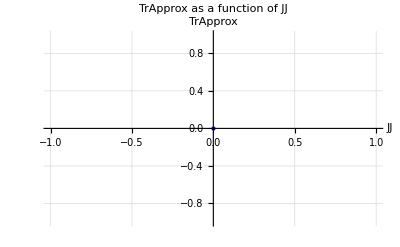

```mathematica
(*Imposta i valori di j e JJ*)
nQubs=4;
jj=2^(nQubs-1);

(*Calcola i valori di TrApprox per tutti i JJ da 0 a 2*jj*)
JJValues=Range[0,2*jj];

(*Parallelizza il calcolo esternamente*)
TrAxCompleteResults=ParallelMap[TrAxComplete[jj,#]&,JJValues];

(*Stampa i risultati per j e JJ*)
Do[Print["j = ",jj,", J = ",JJValues[[i]],", TrComplete = ",TrAxCompleteResults[[i]]],{i,Length[JJValues]}];

(*Crea il grafico di TrApprox in base a JJ*)
ListPlot[Transpose[{JJValues,TrAxCompleteResults}],PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"JJ","TrApprox"},PlotLabel->"TrApprox as a function of JJ",GridLines->Automatic]
```